```mathematica
SetDirectory[NotebookDirectory[]]
```

F:\Dropbox\ClimateData\AmazonBasin\CWD

```mathematica
data = Import["CHRIPS_AB_monthly_05CWD.nc", {"Datasets", "cwd"}];
```

{0.,0.,0.,0.,0.,-7.99341,-37.3581,-101.377,-95.6357,0.,0.,0.,0.,0.,0.,0.,0.,-33.0064,-63.5421,-98.1283,-122.716,0.,0.,0.,0.,0.,0.,0.,0.,0.,-66.7984,-77.6309,-74.8276,0.,0.,0.,0.,0.,0.,0.,0.,-23.5517,-45.2112,-71.3153,-80.0548,0.,0.,0.,0.,0.,0.,0.,0.,-40.4289,-105.437,-159.96,-178.283,0.,0.,0.,0.,0.,0.,0.,0.,-29.9844,-70.5988,-107.023,-130.453,0.,0.,0.,0.,0.,0.,0.,0.,-51.2011,-75.5211,-119.038,-135.305,0.,0.,0.,0.,0.,0.,0.,0.,-41.8149,-94.7977,-134.348,-147.248,0.,0.,0.,0.,0.,0.,0.,0.,0.,-56.2151,-102.655,-133.851,0.,0.,0.,0.,0.,0.,0.,0.,-36.4327,-81.0863,-141.188,-154.736,0.,0.,0.,0.,0.,0.,0.,0.,-37.281,-85.5867,-123.257,-117.787,0.,0.,0.,0.,0.,0.,0.,0.,-12.5152,-62.8321,-117.838,-121.759,0.,0.,0.,0.,0.,0.,0.,0.,0.,-25.0016,-37.5412,-39.7634,0.,0.,0.,0.,0.,0.,0.,0.,-12.2351,-68.0371,-85.7987,-107.093,0.,0.,0.,0.,0.,0.,0.,0.,-28.0856,-69.8828,-114.861,-158.424,0.,0.,0.,0.,0.,0.,0.,0.,-28.3604,-84.2911,-106.201,-86.1364,0.,0.,0.,0.,0.,0.,0.,0.,-22.6782,-92.5833,-119.979,-123.438,0.,0.,0.}

204

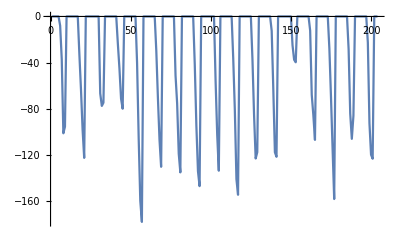

```mathematica
qData = Quantile[data, 0.5];

mqData = qData[[(2001-1981)*12+1;;(2017-1981+1)*12]]

Length[mqData]

ListLinePlot[mqData]
```

```mathematica
data[[1,(2001-1981)*12+1;;(2016-1981+1)*12]]
```

{0.,0.,0.,-40.3602,-124.959,-218.22,-315.33,-402.727,-477.59,-54.2209,-97.9963,-120.158,-128.103,-22.3237,0.,-16.6266,-100.597,-192.238,-281.85,-369.779,-459.822,-34.7997,-52.8135,-37.2656,0.,0.,0.,-62.7583,-153.646,-246.747,-341.819,-431.952,-522.973,-54.7196,-90.784,0.,-10.8274,0.,0.,-25.8751,-115.31,-208.67,-302.333,-387.861,-470.131,-80.7381,-111.085,-66.1607,0.,0.,0.,-17.9458,-105.495,-196.729,-293.417,-383.894,-468.409,-60.4253,-83.4713,0.,0.,0.,0.,-6.99992,-97.1431,-190.147,-283.773,-370.056,-456.957,-42.3939,-62.572,0.,0.,0.,0.,-42.8613,-126.064,-219.041,-313.746,-400.995,-471.975,-51.4678,-79.6482,0.,0.,0.,0.,-50.4862,-141.946,-234.099,-331.165,-422.405,-514.108,-69.6032,-90.5315,-21.2612,0.,0.,0.,-44.1871,-126.785,-219.479,-315.309,-405.399,-490.306,-75.3275,-68.5341,0.,0.,0.,-18.097,-79.9674,-165.607,-257.467,-353.982,-439.105,-529.306,-83.0954,-152.534,-119.887,-113.834,0.,-18.0738,-67.3545,-158.97,-249.762,-346.212,-436.807,-529.619,-73.2412,-131.819,-37.3039,0.,0.,0.,0.,-86.663,-178.45,-274.96,-366.661,-456.883,-74.1908,-64.0278,0.,0.,0.,0.,-74.2877,-160.985,-250.911,-348.222,-434.609,-517.013,-71.1155,-119.962,-103.297,0.,0.,-22.3852,-41.8467,-132.72,-225.749,-323.025,-414.251,-495.434,-47.2469,-73.2651,-22.043,0.,0.,0.,-27.0967,-118.51,-211.587,-306.126,-395.154,-483.255,-79.7378,-111.687,-19.7926,0.,0.,-60.2307,-88.731,-175.836,-263.438,-360.267,-448.8,-536.548,-71.5243,-99.5626,-62.5488}

```mathematica
2001-1982
```

19

```mathematica
dataMCWD =Import["F:\\Dropbox\\ClimateData\\AmazonBasin\\MCWD\\CHRIPS_AB_Monthly_05_mcwd.nc" ,{"Datasets", "mcwd"}];
```

```mathematica
dataMCWD[[1,2001-1982+1]]
```

-477.59